# XX: Making Zeros

We had some questions about how to make various zero patterns.  Lets talk about the middle one.

We were asked if we could transform a general 3×3 matrix A to the following pattern (x | x | 0
x | 0 | x
0 | x | x). This may not be how it was intended to be done but it works!

Compute the SVD A=U.Σ.Vᵀ we now have a two sided orthogonal transformation to the pattern (x | 0 | 0
0 | x | 0
0 | 0 | x) with lots of zeros!

The orthogonal row op (0 | 1 | 0
-1 | 0 | 0
0 | 0 | 1) uses only the top two rows and zeros the diagonal entries  The result is a pattern (0 | x | 0
x | 0 | 0
0 | 0 | x) which has a lot more zeros than asked for.

{True,True}

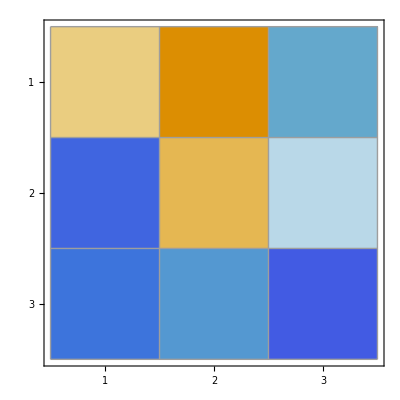
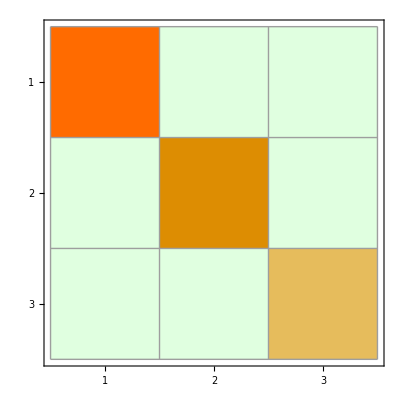
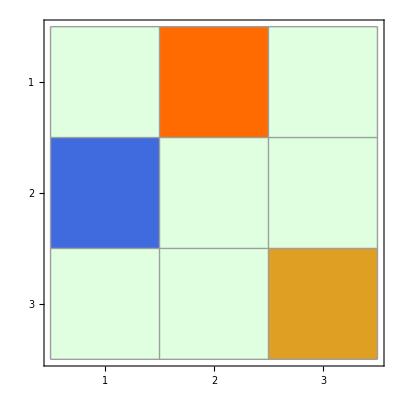

```mathematica
A=RandomReal[{-1,1},{3,3}];
{U,S,V}=SingularValueDecomposition[A];
Q=({{0, 1, 0}, {-1, 0, 0}, {0, 0, 1}}); Map[OrthogonalMatrixQ,{Q.Uᵀ,V}]
Map[MatrixPlot[#,Mesh->All]&,{A,Chop[Uᵀ.A.V],Chop[Q.Uᵀ.A.V]}]
```